```mathematica
equaiton = (λ/(2  Pi)+omega/2) Q^2+deltaPref Q - deltaPref==0
```

-deltaPref+deltaPref Q+Q^2 (omega/2+λ/(2 π))==0

```mathematica
equaiton =  Q^2+deltaPref Q - deltaPref==0
```

-deltaPref+deltaPref Q+Q^2==0

```mathematica
FindInstance[equaiton,{deltaPref,Q}]
```

{{deltaPref→0,Q→0}}

```mathematica
sol = Solve[equaiton, Q]//FullSimplify
```

{{Q→-1/2 √deltaPref (√deltaPref+√(4+deltaPref))},{Q→1/2 (-deltaPref+√deltaPref √(4+deltaPref))}}

```mathematica
sol[[1,1,2]]
```

-1/2 √deltaPref (√deltaPref+√(4+deltaPref))

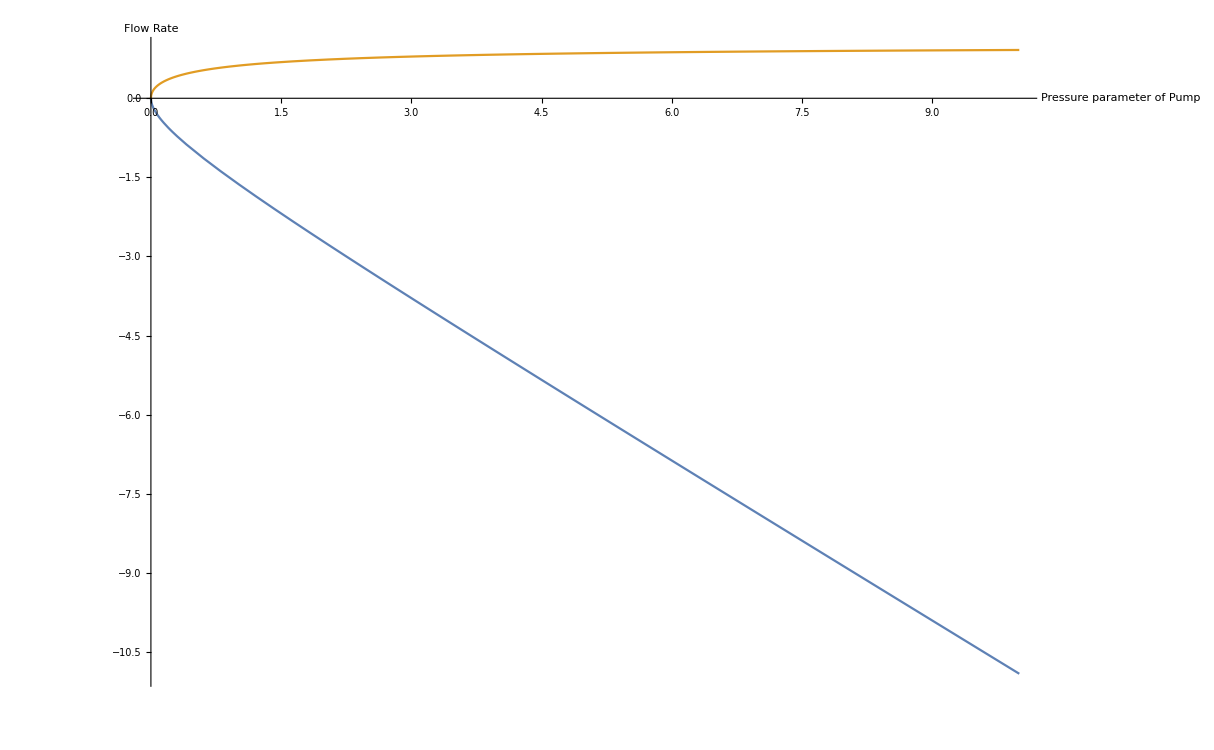

```mathematica
Plot[{-1/2 √deltaPref (√deltaPref+√(4+deltaPref)),1/2 (-deltaPref+√deltaPref √(4+deltaPref) )},{deltaPref, 0, 10},AxesLabel->{"Pressure parameter of Pump","Flow Rate"}]
```

```mathematica
1/2 (-deltaPref+√deltaPref √(4+deltaPref) )/.{deltaPref->10000000000}//N
```

1.

```mathematica
Limit[-1/2 √deltaPref (√deltaPref+√(4+deltaPref))+deltaPref+1, deltaPref->Infinity]
```

0.

```mathematica
Solve[x^2+x-1==0,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
(0.6180339887498949-1.618033988749895)/2
```

-0.5

```mathematica
Integrate[1/(1-Q-Q^2),Q]
```

```mathematica
Solve[-(Log[-1+√5-2 Q]-Log[1+√5+2 Q])/(√5)==t,Q]
```

```mathematica
{{Q->-(1+√5+ⅇ^(√5 t)-√5 ⅇ^(√5 t))/(2 (1+ⅇ^(√5 t)))}}
```

{{Q→-(1+√5+ⅇ^(√5 t)-√5 ⅇ^(√5 t))/(2 (1+ⅇ^(√5 t)))}}

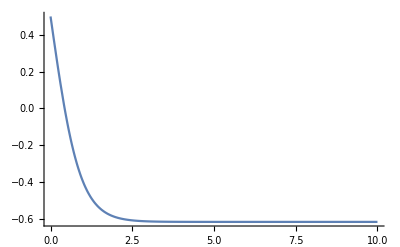

```mathematica
Plot[(1+√5+ⅇ^(√5 t)-√5 ⅇ^(√5 t))/(2 (1+ⅇ^(√5 t))), {t, 0, 10},PlotRange->All]
```

## haha wrong equation!

```mathematica
sol=DSolve[Q'[t]==1/(1-Q[t]-Q[t]^2),Q[t],t]/.{Subscript[c, 1]->1}
```

{{Q[t]→-1/2+15/(2^(2/3) (-378-648 t+648 C[1]+√(-364500+(-378-648 t+648 C[1])^2))^(1/3))+((-378-648 t+648 C[1]+√(-364500+(-378-648 t+648 C[1])^2))^(1/3))/(6 2^(1/3))},{Q[t]→-1/2-(15 (1+ⅈ √3))/(2 2^(2/3) (-378-648 t+648 C[1]+√(-364500+(-378-648 t+648 C[1])^2))^(1/3))-((1-ⅈ √3) (-378-648 t+648 C[1]+√(-364500+(-378-648 t+648 C[1])^2))^(1/3))/(12 2^(1/3))},{Q[t]→-1/2-(15 (1-ⅈ √3))/(2 2^(2/3) (-378-648 t+648 C[1]+√(-364500+(-378-648 t+648 C[1])^2))^(1/3))-((1+ⅈ √3) (-378-648 t+648 C[1]+√(-364500+(-378-648 t+648 C[1])^2))^(1/3))/(12 2^(1/3))}}

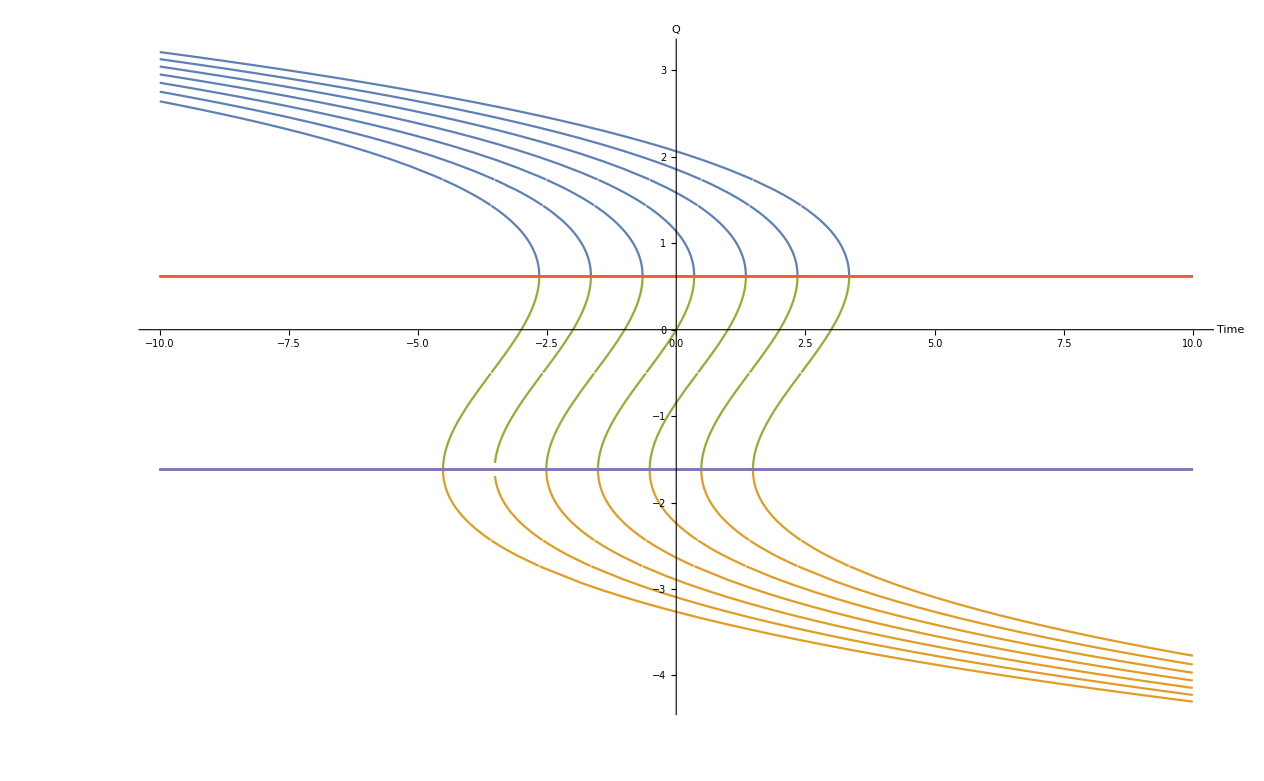

```mathematica
Show@Table[
Plot[{
-1/2+15/(2^(2/3) (-378-648 t+648 c +√(-364500+(-378-648 t+648 c)^2))^(1/3))+((-378-648 t+648 c +√(-364500+(-378-648 t+648 c)^2))^(1/3))/(6 2^(1/3)),-1/2-(15 (1+ⅈ √3))/(2 2^(2/3) (-378-648 t+648 c +√(-364500+(-378-648 t+648 c)^2))^(1/3))-((1-ⅈ √3) (-378-648 t+648 c +√(-364500+(-378-648 t+648 c )^2))^(1/3))/(12 2^(1/3)),
-1/2-(15 (1-ⅈ √3))/(2 2^(2/3) (-378-648 t+648 c +√(-364500+(-378-648 t+648 c)^2))^(1/3))-((1+ⅈ √3) (-378-648 t+648 c +√(-364500+(-378-648 t+648 c)^2))^(1/3))/(12 2^(1/3)),
(-1+√5)/2,(-1-√5)/2},
{t, -10, 10},
PlotRange->All,
WorkingPrecision->5,
AxesLabel->{"Time","Q"}],
{c, -3, 3 }
]
```

```mathematica
sol=DSolveValue[{Q'[t]==1-Q[t]-Q[t]^2,Q[0]==-3},Q[t],t]
```

(-5-3 √5+5 ⅇ^(√5 t)-3 √5 ⅇ^(√5 t))/(5+√5-5 ⅇ^(√5 t)+√5 ⅇ^(√5 t))

```mathematica
Limit[sol, t->Infinity]
```

-1/2+(√5)/2

```mathematica
Limit[sol, t->-Infinity]
```

1/2 (-1-√5)

```mathematica
1/(√5)//N
```

0.447214

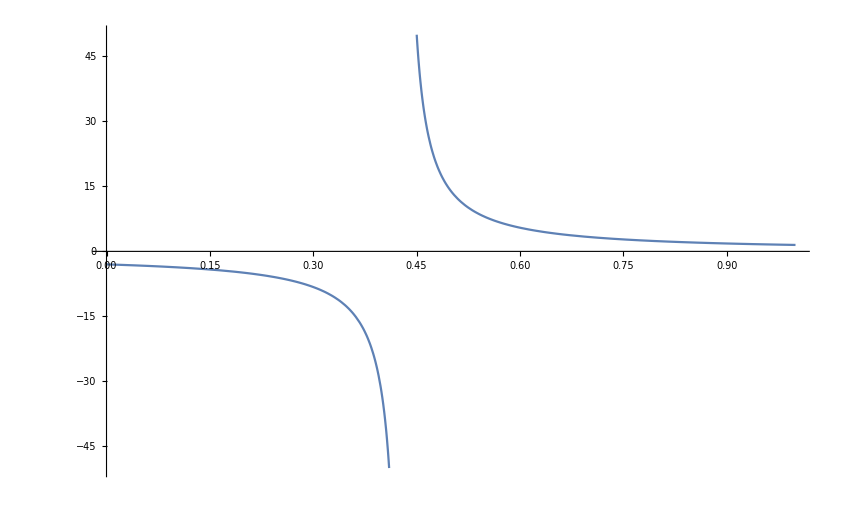

```mathematica
Plot[sol, {t, 0, 1},PlotRange->{{0, 1}, {-50, 50}}]
```

```mathematica
(-1-√5)/2//N
```

-1.61803

```mathematica
sol=DSolveValue[{Q'[t]==1-Q[t]-Q[t]^2,Q[0]==(-1-√5)/2+0.01},Q[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(0.5 (-720.371+1.23607 ⅇ^(√5 t)))/(222.607+ⅇ^(√5 t))

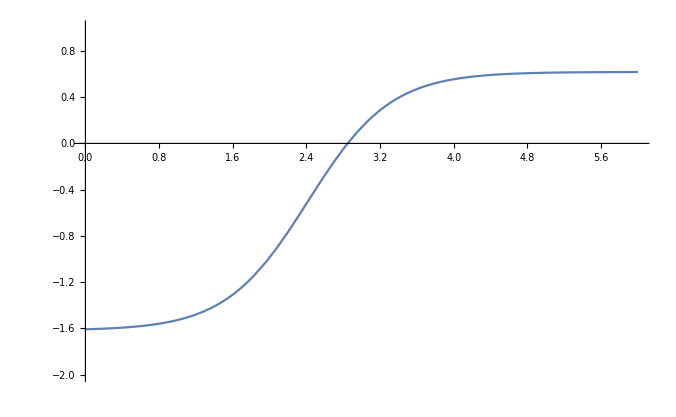

```mathematica
Plot[sol, {t, 0, 6},PlotRange->{{0, 6}, {-2, 1}}]
```

```mathematica
qRange={-2, (-1-√5)/2, (-1-√5)/2+1/100, 0,(-1+√5)/2,1, 2};
sols=Table[DSolveValue[{Q'[t]==1-Q[t]-Q[t]^2,Q[0]==q0},Q[t],t],{q0, qRange}]
```

{-(2 (2+√5-2 ⅇ^(√5 t)+√5 ⅇ^(√5 t)))/(3+√5-3 ⅇ^(√5 t)+√5 ⅇ^(√5 t)),1/2 (-1-√5),(-499-99 √5-ⅇ^(√5 t)+√5 ⅇ^(√5 t))/(2 (-1+100 √5+ⅇ^(√5 t))),(2 (-1+ⅇ^(√5 t)))/(-1+√5+ⅇ^(√5 t)+√5 ⅇ^(√5 t)),1/2 (-1+√5),(-1+√5+ⅇ^(√5 t)+√5 ⅇ^(√5 t))/(-3+√5+3 ⅇ^(√5 t)+√5 ⅇ^(√5 t)),(2 √5 (1+ⅇ^(√5 t)))/(-5+√5+5 ⅇ^(√5 t)+√5 ⅇ^(√5 t))}

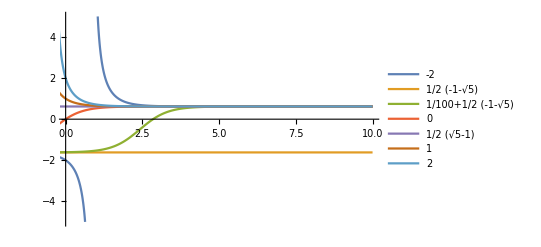

```mathematica
Plot[sols,{t,-4, 10},PlotRange->{{0, 10}, {-5, 5}},PlotLegends->qRange]
```

### DAY 2.

```mathematica
Reduce[]
```

```mathematica
sol = DSolveValue[{Q'[t]==c+b Q[t]+a Q[t]^2},Q[t],t]//FullSimplify
```

(-b+√(-b^2+4 a c) Tan[1/2 √(-b^2+4 a c) (t+C[1])])/(2 a)

```mathematica
(-b+√(-b^2+4 a c) Tan[1/2 (√(-b^2+4 a c) t+√(-b^2+4 a c) k)])/(2 a)
```

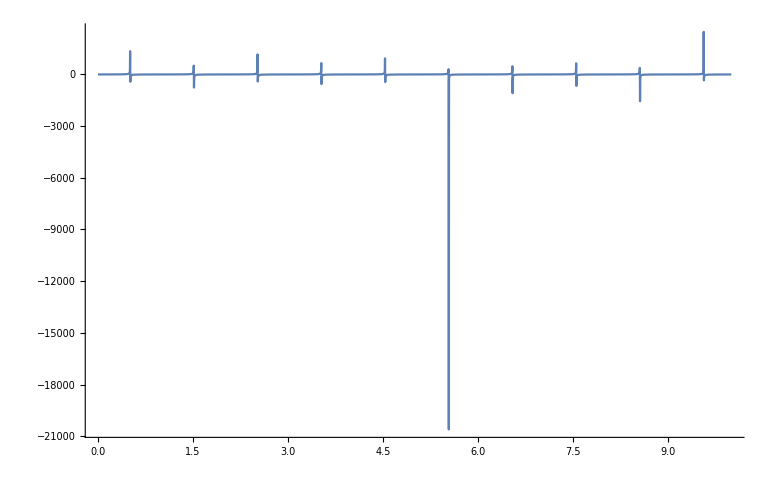

```mathematica
Plot[(-b+√(-b^2+4 a c) Tan[1/2 (√(-b^2+4 a c) t+√(-b^2+4 a c) k)])/(2 a)/.{c->10, b->-1, a->1, k->1},{t, 0, 10},PlotRange->All]
```

```mathematica
sol/.{c->10, b->-1, a->1}
```

1/2 (1+√39 Tan[1/2 (√39 t+√39 C[1])])

# Test of solution using force and only pressure

```mathematica
Solve[deltaPref (1-Q/Qmax)==1/(2 ro)(lambda(L1/S1^2+L2/S2^2)+eta/Svalve^2)Q^2,Q]
```

{{Q→(-deltaPref/Qmax-√(deltaPref^2/Qmax^2+(2 deltaPref L1 lambda)/(ro S1^2)+(2 deltaPref L2 lambda)/(ro S2^2)+(2 deltaPref eta)/(ro Svalve^2)))/((L1 lambda)/(ro S1^2)+(L2 lambda)/(ro S2^2)+eta/(ro Svalve^2))},{Q→(-deltaPref/Qmax+√(deltaPref^2/Qmax^2+(2 deltaPref L1 lambda)/(ro S1^2)+(2 deltaPref L2 lambda)/(ro S2^2)+(2 deltaPref eta)/(ro Svalve^2)))/((L1 lambda)/(ro S1^2)+(L2 lambda)/(ro S2^2)+eta/(ro Svalve^2))}}

```mathematica
Solve[(2 S1 S2)/(S1+S2)deltaPref (1-Q/Qmax)==1/(2 ro)(lambda(L1/S1+L2/S2)+(2S1 S2)/(S1+S2)eta/Svalve^2)Q^2,Q]//FullSimplify
```

{{Q→(2 ro S1 S2 Svalve^2 (-deltaPref S1 S2+Qmax (S1+S2) √((deltaPref (deltaPref ro S1^2 S2^2 Svalve^2+Qmax^2 (2 eta S1^2 S2^2+lambda (S1+S2) (L2 S1+L1 S2) Svalve^2)))/(Qmax^2 ro (S1+S2)^2 Svalve^2))))/(2 eta Qmax S1^2 S2^2+lambda Qmax (S1+S2) (L2 S1+L1 S2) Svalve^2)},{Q→-(2 ro S1 S2 Svalve^2 (deltaPref S1 S2+Qmax (S1+S2) √((deltaPref (deltaPref ro S1^2 S2^2 Svalve^2+Qmax^2 (2 eta S1^2 S2^2+lambda (S1+S2) (L2 S1+L1 S2) Svalve^2)))/(Qmax^2 ro (S1+S2)^2 Svalve^2))))/(2 eta Qmax S1^2 S2^2+lambda Qmax (S1+S2) (L2 S1+L1 S2) Svalve^2)}}

```mathematica
Solve[(2 ro deltaPref Svalve^2)/eta(1 - Q/Qmax)==Q^2,Q]//FullSimplify
```

{{Q→-(deltaPref ro Svalve^2+√(deltaPref ro Svalve^2 (2 eta Qmax^2+deltaPref ro Svalve^2)))/(eta Qmax)},{Q→(-deltaPref ro Svalve^2+√(deltaPref ro Svalve^2 (2 eta Qmax^2+deltaPref ro Svalve^2)))/(eta Qmax)}}